```mathematica
grad[J_,X_,Y_,a_,j_]:=Block[{tt={},m=Length[X],t,θ=Table[0,{g,1,Length@X[[1]]}]},
AppendTo[tt,J[θ]];
For[i=1,i≤j,i++,
t=(X.θ-Y);
For[h=1,h≤Length@X[[1]],h++,θ[[h]]=θ[[h]]-a 1/m Sum[t[[g]]X[[g,h]],{g,1,m}];];
AppendTo[tt,J[θ]];];
{θ,Flatten@tt}]
```

```mathematica
data={{2104,3,399900},{1600,3,329900},{2400,3,369000},{1416,2,232000},{3000,4,539900},{1985,4,299900},{1534,3,314900},{1427,3,198999},{1380,3,212000},{1494,3,242500},{1940,4,239999},{2000,3,347000},{1890,3,329999},{4478,5,699900},{1268,3,259900},{2300,4,449900},{1320,2,299900},{1236,3,199900},{2609,4,499998},{3031,4,599000},{1767,3,252900},{1888,2,255000},{1604,3,242900},{1962,4,259900},{3890,3,573900},{1100,3,249900},{1458,3,464500},{2526,3,469000},{2200,3,475000},{2637,3,299900},{1839,2,349900},{1000,1,169900},{2040,4,314900},{3137,3,579900},{1811,4,285900},{1437,3,249900},{1239,3,229900},{2132,4,345000},{4215,4,549000},{2162,4,287000},{1664,2,368500},{2238,3,329900},{2567,4,314000},{1200,3,299000},{852,2,179900},{1852,4,299900},{1203,3,239500}};
```

```mathematica
scaling[xx_]:=(xx-Total[data[[;;,1]]]/Length[data])/(Max[data[[;;,1]]]-Min[data[[;;,1]]])
antiscaling[x_]:=Max[data[[;;,1]]]-Min[data[[;;,1]]]*x+Total[data[[;;,1]]]/Length[data]
```

```mathematica
X=Table[{1,scaling[data[[i,1]]],data[[i,2]]},{i,1,Length[data]}]//N;
Y=Table[{data[[i,3]]},{i,1,Length[data]}];
```

```mathematica
J:=1/(2Length[X])(X.#-Y)ᵀ.(X.#-Y)&
```

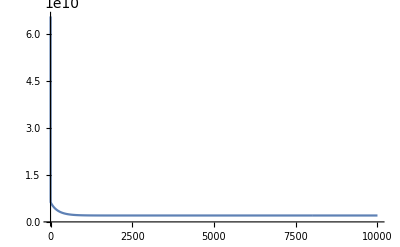

```mathematica
θ=grad[1/(2Length[X])(X.#-Y)ᵀ.(X.#-Y)&,X,Y,0.1,10000];
ListLinePlot[θ[[2]],PlotRange->All]
```

```mathematica
θ1=θ[[1]]
θ2=Inverse[(Xᵀ.X)].Xᵀ.Y
```

{{368114.},{504778.},{-8738.02}}

{{368114.},{504778.},{-8738.02}}

```mathematica
f1[x_,y_]:=θ1ᵀ.{1,scaling[x],y}
f2[x_,y_]:=(θ2ᵀ.{1,scaling[x],y})
```

```mathematica
Show[Plot3D[{f1[x,y],f2[x,y]},{x,1000,5000},{y,2,4}],ListPointPlot3D[data,Filling->Bottom,PlotStyle->{ PointSize[Large]}]]
```

-Graphics3D-